```mathematica
Zdol=((r2+s*L)^-1+s*c )^-1
```

1/(1/(1.62+0.01968 s)+2.2×10^-6 s)

```mathematica
k=FullSimplify[Zdol/(Zdol+R)]
```

(24139.9+293.255 s)/(2.3121×10^7+s (375.572+1. s))

```mathematica
impulseresponse=Simplify[TrigReduce[ComplexExpand[Simplify[InverseLaplaceTransform[k, s, t]]]]]
```

ⅇ^(-187.786 t) ((293.255+1.77636×10^-15 ⅈ) Cos[(4804.76+0. ⅈ) t]-(6.43723+8.52651×10^-14 ⅈ) Sin[(4804.76+0. ⅈ) t])

```mathematica
293.2551319648095Cos[4804.757867067572t]-6.437230551412924Sin[4804.757867067572t]
```

293.255 Cos[4804.76 t]-6.43723 Sin[4804.76 t]

293.255 Cos[4804.76 t]-(6.43723+5.68434×10^-14 ⅈ) Sin[4804.76 t]

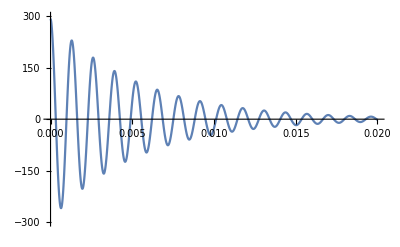

```mathematica
Plot[impulseresponse,{t, 0, 0.02}, PlotRange->{-300,300}]
```

```mathematica
stepresponse=Simplify[TrigReduce[ComplexExpand[Simplify[InverseLaplaceTransform[k/s, s, t]]]]]
```

0.00104407-0.00104407 ⅇ^(-187.786 t) Cos[(4804.76+0. ⅈ) t]+0.0609935 ⅇ^(-187.786 t) Sin[(4804.76+0. ⅈ) t]

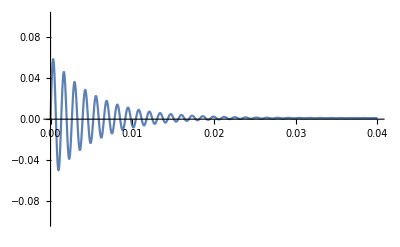

```mathematica
Plot[stepresponse,{t, 0,0.04}, PlotRange->{-0.1,0.1}]
```

```mathematica
R=1550
```

1550

```mathematica
r2=1.62
```

1.62

```mathematica
c=2.2*10^-6
```

2.2×10^-6

```mathematica
L=19.68*10^-3
```

0.01968

```mathematica
Simplify[ComplexExpand[impulseresponse]]
```

ⅇ^(-187.786 t) (Sin[0.-4804.76 t] ((3.21862+146.628 ⅈ)-(3.21862-146.628 ⅈ) Cos[(9609.52+0. ⅈ) t]-(146.628+3.21862 ⅈ) Sin[(9609.52+0. ⅈ) t])+Cos[(4804.76+0. ⅈ) t] ((146.628-3.21862 ⅈ)+(146.628+3.21862 ⅈ) Cos[(9609.52+0. ⅈ) t]-(3.21862-146.628 ⅈ) Sin[(9609.52+0. ⅈ) t]))

```mathematica
Zdoldrugie=((r2+I*w*L)^-1+I*w*c )^-1
kdrugie=FullSimplify[Zdol/(Zdol+R)]
```

1/(1/(1.62+(0.+0.01968 ⅈ) w)+(0.+2.2×10^-6 ⅈ) w)

(-24139.9-(0.+293.255 ⅈ) w)/(-2.3121×10^7+w ((0.-375.572 ⅈ)+1. w))

```mathematica
ExpandDenominator[kdrugie]
```

(-24139.9-(0.+293.255 ⅈ) w)/(-2.3121×10^7-(0.+375.572 ⅈ) w+1. w^2)